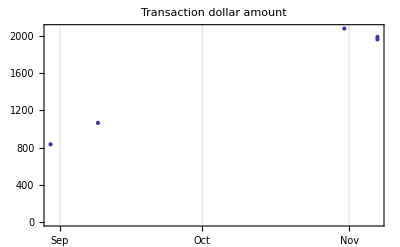

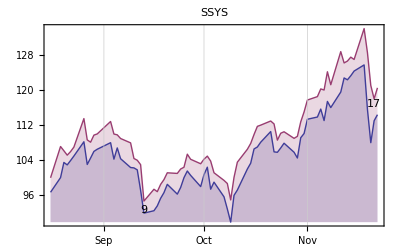

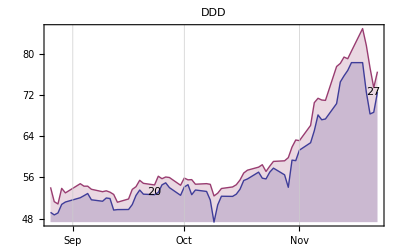

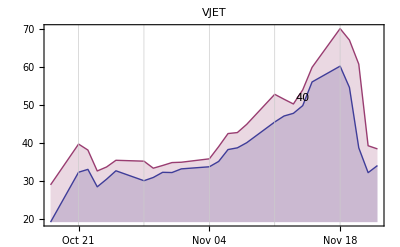

```mathematica
(* FinanceData[] doesn't appear to have Canadian listings: CJR.B, or the symbol is different *)
Clear[ txCanadian ]
txCanadian = {"CJR.B",40,22.500,{2012,7,23,0,0,0}} ;

(* {symbol, shares, price, DateList[]} *)
Clear[ tx ]
tx = {
{"SSYS",9,92.750,{2013,9,13, 0}},{"DDD",20,53.260,{2013,9,23, 0}},{"VJET",40,51.930,{2013,11,14, 0}},{"DDD",27,72.600,{2013,11,21, 0}},{"SSYS",17,116.920,{2013,11,21, 0}}
} ;

(* These subselections should be possible programatically *)
Clear[ ssys, ddd, vjet ] 
ssys = {tx[[1]], tx[[5]]} ;
ddd = {tx[[2]], tx[[4]]} ;
vjet = {tx[[3]]} ;

Module[{nWeeks},
nWeeks = 2 ;
DateListPlot[{#[[4]] - {0, 0, 0, 24*7*nWeeks} , #[[2]]*#[[3]]} &/@ tx,
PlotRange -> Full, PlotLabel -> "Transaction dollar amount"]
]

historyAndPoints[l_] := Module[{oldestTx, n},
oldestTx = l[[1]] ;
n = 4 ;
DateListPlot[ 
FinancialData[ oldestTx[[1]], #,oldestTx[[4]] -{0, 0, 0, 24*7*4}] &/@ {"Low", "High"}
, PlotLabel -> oldestTx[[1]]
, Joined -> True
, Filling->Bottom
, Epilog ->  Flatten[
Tooltip[
Text[#[[2]],{#[[4]],#[[3]]}]
, Row[{
#[[3]], " ($", #[[2]]*#[[3]],")"
}] 
]&/@ l, 1]
] 
]
historyAndPoints[ ssys ]
historyAndPoints[ ddd ]
historyAndPoints[ vjet ]
```